```mathematica
length=eigensystem[0][[1]]//Length;
Table[
Table[
{i dk, -initShift+eigensystem[i dk][[1]][[j]]},
{j,1,length}
],
{i,0,numPartitions}
];
```

```mathematica
list=Table[
{i dk,-initShift+ eigensystem[i dk][[1]][[j]]},
{j,1,length},
{i,0,numPartitions}
];
```

```mathematica
FermiLine = Table[{i dk,EFermi},{i,0,numPartitions}];
```

Part::partw: Part 8 of {2., 4., 4., 4., 2., 4., 2.} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

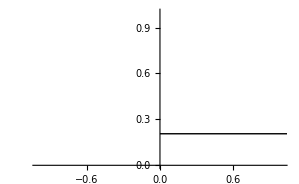

```mathematica
f1=ListPlot[list,Joined-> True,Mesh-> All,PlotRange-> {0,1}];
f2 = ListPlot[FermiLine,Joined-> True,PlotRange-> {0,1},PlotStyle-> {Thick,Black}];
Show[f1,f2]
```

Part::partw: Part 8 of {2., 4., 4., 4., 2., 4., 2.} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

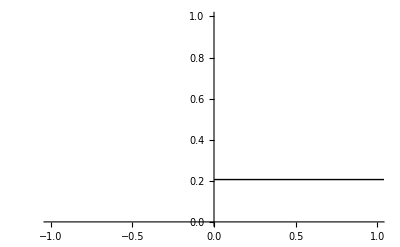

```mathematica
BandStructure[]
```